Forces on a Partially Submerged Gate

```mathematica
Manipulate[
Module[{conv1,conv2,h0,a1,a2,w,h2,h1,b,A,yc,hc,Ixc,yR,hR,γ,W,FR,FT,xc,xR,scale,units,FTmax,δ,labels},
conv1=If[tab==1,1,0.3048];(*ft to m*)
conv2=If[tab==1,1,4.448];(*lbF to N*)

h0=If[tab==1,hA,hB];
a1=h1/Sin[θ];(*The length of the gate that has force from water acted upon it, m or ft*)
a2=8*conv1;(*Total length of gate - 8 ft*)
w=4*conv1;(*Height of water - 4 ft*)
h2=a2*Sin[θ];(*Height of edge of gate*)
h1=If[h0≥h2,h2,h0];(*water height*)

b=3.28084*conv1;(*Length of the gate, ft, m*)
A=a1*b;(*Area of gate with force from water acted upon it*)
yc=a1/2;
hc=yc*Sin[θ];(*1/2 of h1, m or ft*)

Ixc=1/12*b*a1^3;
yR=Ixc/(yc*A)+yc;
hR=yR*Sin[θ];

γ=If[tab==1,62.43,9807];(*specific gravity, Subscript[lb, f]/ft^3, N/m^3*)
W=If[tab==1,WA,WB]*1000;(*weight lbF, kN*)

(*Correction: I corrected the FR equation and FT equation. Just used the equations in the "details" section - Neil*)
FR=γ*Sin[θ]*A*a1/2;
FT=(FR*a1/3+W*a2/2*Cos[θ])/(a2*Sin[θ]);

xc=x/.Quiet@Solve[0.5*a2*Sin[θ]==(h2-0)/(w+a2*Cos[θ]-w)*(x-w)+0,x][[1]];
xR=x/.Quiet@Solve[0.333*h1==(h2-0)/(w+a2*Cos[θ]-w)*(x-w)+0,x][[1]];

scale[F_]:=If[tab==1,1.75*Rescale[F,{-1000,5000}],0.53*Rescale[F,{-5000,22200}]];
units=If[tab==1,Subscript[" klb","F"]," kN"];
FTmax=FT<4232*conv2;If[FTmax==False,label=False];

δ=1.2*If[tab==1,0.85,0.26];


labels=If[label,{Thin,
(*WATER HEIGHT*)
Line[{{0.25*w,0},{0.25*w,h1}}],
Text[Framed[Style[Row@{NumberForm[h1,{3,2}],If[tab==1," ft"," m"]},17],Background->RGBColor[0.6,1,0.95],FrameStyle->None,FrameMargins->Tiny],{0.25*w,0.25*h1}],

(*GATE HEIGHT*)
Line[{{0.6*w,0},{0.6*w,h2}}],
Text[Framed[Style[Row@{NumberForm[N@h2,{4,2}],If[tab==1," ft"," m"]},17],Background->RGBColor[0.6,1,0.95],FrameStyle->None,FrameMargins->Tiny],{0.6*w,0.25*h1}],

(*WATER LENGTH*)
Line[{{w+δ,0},{w+a1*Cos[θ]+δ,h1}}],Line[{w+#*δ,0}&/@{0.8,1.2}],Line[{w+a1*Cos[θ]+#*δ,h1}&/@{0.8,1.2}],
Text[Framed[Style[Row@{NumberForm[N@a1,{3,2}],If[tab==1," ft"," m"]},17],Background->White,FrameStyle->None,FrameMargins->Tiny],{w+0.7*a1*Cos[θ]+δ,0.7*h1}],

(*GATE LENGTH*)
Line[{{w+2*δ,0},{w+a2*Cos[θ]+2*δ,h2}}],Line[{w+2*δ+#*0.2*δ,0}&/@{-1,1}],Line[{w+a2*Cos[θ]+2*δ+#*0.2*δ,h2}&/@{-1,1}],
Text[Framed[Style[Row@{NumberForm[a2,{3,2}],If[tab==1," ft"," m"]},17],Background->White,FrameStyle->None,FrameMargins->Tiny],{w+0.7*a2*Cos[θ]+2*δ,0.7*h2}],

(*FORCE HEIGHT*)
Line[{{0.75*xR,0},{0.75*xR,1/3 h1}}],Line[{{0.75*xR,1/3 h1},{xR,1/3 h1}}],Line[{{0.75*xR+0.2*δ,1/3 h1},{0.75*xR-0.2*δ,1/3 h1}}],
Text[Framed[Style[Row@{NumberForm[N@h1/3,2]," m"},17],Background->RGBColor[0.6,1,0.95],FrameStyle->None,FrameMargins->Tiny],{0.75*xR,0.5*0.333*h1}],

(*ANGLE*)
Line[{{w,0},{1.15*w,0}}],Circle[{w,0},If[tab==1,0.5,0.155],{0,θ}],
Text[Style[θ,17,Background->White],{w,0},{-3,-1}]
}];

Graphics[{Thick,Arrowheads@0.045,
(*ground lines*)
{Thin,If[tab==1,Line[{{#,-0.5},{#+0.5,0}}]&/@Range[0,w-0.5,0.5],Line[{{#,-0.15},{#+0.15,0}}]&/@Range[0,w-0.15,0.15]]},

(*structure*)
If[FTmax,{{FaceForm@RGBColor[0.6,1,0.95],Polygon[{{0,h1},{0,0},{w,0},{w+h1/Sin[θ]*Cos[θ],h1}}]},Line[{{0,h2},{w+a2*Cos[θ],h2}}]}],
{CapForm@None,
Thickness@0.015,Line[{{0,1.1*h2},{0,0},{w,0}}],
{Thickness@0.03,GrayLevel@0.6,If[FTmax,Line[{{w,0},{w+a2*Cos[θ],h2}}],Line[{{w,0},{2.5*w,0}}]]}},
{PointSize@0.045,Point@{w,0},PointSize@0.035,White,Point@{w,0}},
Text[Framed[Style["hinge",17],Background->White,FrameStyle->None,FrameMargins->Tiny],{w,0},{0,2}],

If[FTmax,labels],

(*TENSION*)
If[FTmax,{
{RGBColor[0,0.6,0],Arrowheads@{{-0.045,0.7},{0.045,0.3}},Arrow[{{w+a2*Cos[θ],h2},{0,h2}}],
Text[Style[Row@{"tension = ",NumberForm[FT/1000,{6,2}],units},18,Background->White],{(w+a2*Cos[θ])/2,h2}]},
{PointSize@0.017,Point@#,White,PointSize@0.015,Point@#}&/@{{0,h2},{w+a2*Cos[θ],h2}},

(*WEIGHT*)
{Blue,Arrow[{{xc,0.5*a2*Sin[θ]},{xc,0.5*a2*Sin[θ]-1.5*scale[W]}}],
If[W>0,Text[Style[Row@{"gate weight = ",NumberForm[N@W/1000,{6,2}],units},18,Background->White],{xc,0.5*a2*Sin[θ]-1.5*scale[W]},{-0.5,1}]],
PointSize@0.017,Point@{xc,0.5*a2*Sin[θ]}},

(*RESULTANT*)
{Purple,
Text[Style[Column[{"force from water",Row@{NumberForm[FR/1000,{6,2}],units}},Center],18,Background->RGBColor[0.6,1,0.95]],{xR+1.2*scale[FR]*Cos[90°+θ],0.333*h1+1.2*scale[FR]*Sin[90°+θ]},0.7*{1,-1}],
Arrow[{{xR+1.2*scale[FR]*Cos[90°+θ],0.333*h1+1.2*scale[FR]*Sin[90°+θ]},{xR,0.333*h1}}],
PointSize@0.017,Point@{xR,0.333*h1}}
}],

If[FTmax==False,Text[Style["cable tension too high; cable snapped",18],If[tab==1,{4.3,6},{1.31,1.83}]]]
},ImageSize->{600,400},PlotRange->If[tab==1,{{0,13.17},{-0.75,7.976}},{{0,4.017},{-0.25,2.431}}],PlotRangePadding->Scaled@0.02]
],
Grid[{
{Control[{{θ,60°,"angle"},30°,65°,1°,Appearance->"Labeled",ImageSize->Small}],
PaneSelector[{
1->Row@{Control[{{hA,4,"water height (ft)"},2.3,4.11,0.1,ImageSize->Small}],Spacer@5,Dynamic@NumberForm[hA,{5,2}]},
2->Row@{Control[{{hB,1.22,"water height (m)"},0.7,1.25,0.01,ImageSize->Small}],Spacer@5,Dynamic@NumberForm[hB,{5,2}]}
},Dynamic@tab],SpanFromLeft},
{PaneSelector[{
1->Row@{Control[{{WA,5,Row@{"gate weight (",Subscript["klb","F"],")"}},0,5,0.1}],Spacer@5,Dynamic@NumberForm[WA,{4,1}]},
2->Row@{Control[{{WB,22.2,"gate weight (kN)"},0,22.24,0.1}],Spacer@5,Dynamic@NumberForm[WB,{4,1}]}
},Dynamic@tab],SpanFromLeft,
Control[{{tab,2},1,2,1,None}],
Button["US customary",{hA=hB/0.3048,WA=WB/4.448,tab=1},Enabled->If[tab==1,False,True]],
Button["SI",{hB=hA*0.3048,WB=WA*4.448,tab=2},Enabled->If[tab==2,False,True]],
Control[{{label,False,"show distances"},{True,False}}]}
},Alignment->Left]
]
```

A gate, which is hinged at the bottom, is partially submerged under water, and a cable holds the gate closed. Use the sliders to set the angle of the gate, the weight of the gate, and the water height. Use the buttons to change the units from klb_F and ft (US customary units) to kN and m (SI units). Check the "show distance" box to display distances. The Demonstration displays the cable tension needed to support the gate. When the tension is too high (greater than 4.23 klb_F or 18.82 kN), the cable breaks.

w::shdw: Symbol w appears in multiple contexts {Notebook$$16$287681`,Global`}; definitions in context Notebook$$16$287681` may shadow or be shadowed by other definitions.

δ::shdw: Symbol δ appears in multiple contexts {Notebook$$16$287681`,Global`}; definitions in context Notebook$$16$287681` may shadow or be shadowed by other definitions.

This Demonstration determines the cable tension necessary to support a gate submerged under water (see Figure 1). The gate is a_2 meters long, and the distance from the hinge to top of the water along the gate is a_1 meters.

The magnitude of the resultant force due to the water is found by summing the differential forces dF=γ h dA over the entire surface:

F_R=∫_A γ h dA=∫_A γ y sin θ dA,

where F_R is the resultant force (N), γ is the specific weight of water (9.807 kN/m^3), h=y sin θ is the vertical distance from the top of the water to any point in the water (m), y is the corresponding distance along the gate (m), θ is the angle of the gate (degrees), ⅆA= b ⅆy is differential area of the gate (m^2), and b is the width of the gate (m). Note that the specific weight γ is the specific gravity ρ times the acceleration of gravity g. The total area of the gate that is in contact with water is A_gate=b a_1. This integral is from y=0 at the top of the water level to y=a_1 at the hinge.

Since γ is constant, and for a fixed value of θ, the resultant force becomes:

F_R=γ sin θ ∫_A y dA.

The integral ∫_A y dA is:

(∫_A y dA= ∫_0^a_1 y b ⅆy=(b y^2)/2|)_0^a_1,

this is then equal to:

∫_A yⅆA=b/2 a_1^2=A_gate a_1/2,

the resultant force is then:

F_R=γ sin θ A_gate a_1/2.

The sum of the moments around the hinge is equal to the moment of the resultant force at the y coordinate y_R. Note that moment is proportional to the distance from the hinge to location of the force:

F_R (a_1-y_R)=∫_A γ y (a_1-y) sin θⅆA=γ sin θ ∫_0^a_1 y (a_1-y) bⅆy=γ sin θ ((a_1 y^2)/2-y^3/3) b,

F_R (a_1-y_R)=γ sin θ (a_1^3/2-a_1^3/3) b=γ sin θ a_1^2/6 A_gate,

and since F_R=γ sin θ A_gate a_1/2,

(a_1 -y_R)=a_1/3.

That is, the resultant force is located 1/3 of the distance from the hinge to the water level along the gate. A moment balance determines the tension T (kN) in the cable that is holding up the gate:

∑M=0=F_R a_1/3+W_gate  a_2/2 cos θ-T a_2 sin θ.

where W_gate is the weight of the gate, which is located at the center of the gate. The tension is then:

T=(F_R a_1/3+W_gate  a_2/2 cos θ)/(a_2 sin θ).

Figure 1

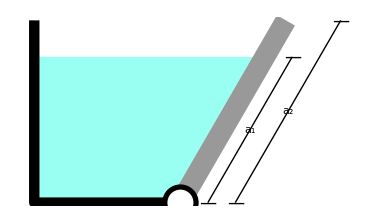

Figure 2

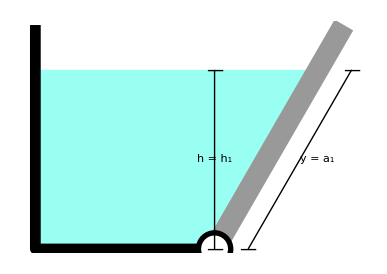

Reference

[1] B. R. Munson, T. H. Okiishi and W. W. Huebsch, Fundamentals of Fluid Mechanics, 6th ed., Hoboken, NJ: John Wiley & Sons, 2009 pp. 57–60.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

chemical engineering

mechanical engineering

fluids

fluids gate

gate

submerged area

submerged gate

fluid mechanics

Forces on a Completely Submerged Gate

Contributed by: Rachael L. Baumann

Additional contributions by: John L. Falconer, Kimberly R. Bourland, and Neil Hendren

(University of Colorado Boulder, Department of Chemical and Biological Engineering)

Global`A::shdw: Symbol A appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`a1::shdw: Symbol a1 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`a2::shdw: Symbol a2 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`b::shdw: Symbol b appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`conv1::shdw: Symbol conv1 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`conv2::shdw: Symbol conv2 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`F::shdw: Symbol F appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FR::shdw: Symbol FR appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FT::shdw: Symbol FT appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FTmax::shdw: Symbol FTmax appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`h0::shdw: Symbol h0 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`h1::shdw: Symbol h1 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`h2::shdw: Symbol h2 appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hA::shdw: Symbol hA appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hB::shdw: Symbol hB appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hc::shdw: Symbol hc appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hR::shdw: Symbol hR appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`Ixc::shdw: Symbol Ixc appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`label::shdw: Symbol label appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`labels::shdw: Symbol labels appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`scale::shdw: Symbol scale appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`tab::shdw: Symbol tab appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`units::shdw: Symbol units appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`W::shdw: Symbol W appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WA::shdw: Symbol WA appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WB::shdw: Symbol WB appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`x::shdw: Symbol x appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`xc::shdw: Symbol xc appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`xR::shdw: Symbol xR appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`yc::shdw: Symbol yc appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`yR::shdw: Symbol yR appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`γ::shdw: Symbol γ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`θ::shdw: Symbol θ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`a1$::shdw: Symbol a1$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`a2$::shdw: Symbol a2$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`A$::shdw: Symbol A$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`b$::shdw: Symbol b$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`conv1$::shdw: Symbol conv1$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`conv2$::shdw: Symbol conv2$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FR$::shdw: Symbol FR$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FTmax$::shdw: Symbol FTmax$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`FT$::shdw: Symbol FT$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`F$::shdw: Symbol F$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`h0$::shdw: Symbol h0$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`h1$::shdw: Symbol h1$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`h2$::shdw: Symbol h2$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hc$::shdw: Symbol hc$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hR$::shdw: Symbol hR$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`Ixc$::shdw: Symbol Ixc$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`labels$::shdw: Symbol labels$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`scale$::shdw: Symbol scale$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`units$::shdw: Symbol units$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`W$::shdw: Symbol W$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`xc$::shdw: Symbol xc$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`xR$::shdw: Symbol xR$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`yc$::shdw: Symbol yc$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`yR$::shdw: Symbol yR$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`γ$::shdw: Symbol γ$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hA$3418$$::shdw: Symbol hA$3418$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hA$$::shdw: Symbol hA$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hB$3419$$::shdw: Symbol hB$3419$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hB$$::shdw: Symbol hB$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`label$3423$$::shdw: Symbol label$3423$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`label$$::shdw: Symbol label$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`tab$3422$$::shdw: Symbol tab$3422$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`tab$$::shdw: Symbol tab$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WA$3420$$::shdw: Symbol WA$3420$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WA$$::shdw: Symbol WA$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WB$3421$$::shdw: Symbol WB$3421$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WB$$::shdw: Symbol WB$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`θ$3417$$::shdw: Symbol θ$3417$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`θ$$::shdw: Symbol θ$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hA$3566$$::shdw: Symbol hA$3566$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hB$3567$$::shdw: Symbol hB$3567$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`label$3571$$::shdw: Symbol label$3571$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`tab$3570$$::shdw: Symbol tab$3570$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WA$3568$$::shdw: Symbol WA$3568$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WB$3569$$::shdw: Symbol WB$3569$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`θ$3565$$::shdw: Symbol θ$3565$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hA$3684$$::shdw: Symbol hA$3684$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hB$3685$$::shdw: Symbol hB$3685$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`label$3689$$::shdw: Symbol label$3689$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`tab$3688$$::shdw: Symbol tab$3688$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WA$3686$$::shdw: Symbol WA$3686$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WB$3687$$::shdw: Symbol WB$3687$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`θ$3683$$::shdw: Symbol θ$3683$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hA$3802$$::shdw: Symbol hA$3802$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`hB$3803$$::shdw: Symbol hB$3803$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`label$3807$$::shdw: Symbol label$3807$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`tab$3806$$::shdw: Symbol tab$3806$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WA$3804$$::shdw: Symbol WA$3804$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`WB$3805$$::shdw: Symbol WB$3805$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.

Global`θ$3801$$::shdw: Symbol θ$3801$$ appears in multiple contexts {Global`,Notebook$$16$287681`}; definitions in context Global` may shadow or be shadowed by other definitions.